## Helium-6

## Elastic scattering

### Import data

```mathematica
imageSize=Small;
gray=GrayLevel[0.66];
thickness=Thickness[0.008];
blue=ColorData[97,"ColorList"]⟦1⟧;
orange=ColorData[97,"ColorList"]⟦2⟧;
```

```mathematica
StringJoin[NotebookDirectory[],"/dcs/6HE4HE.exp"];
expData=Import[%,"Table"];
```

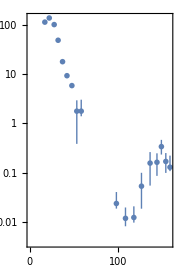

```mathematica
expData;
Map[{#⟦1⟧,Around[#⟦2⟧,{#⟦3⟧,#⟦4⟧}]}&,%];
ListLogPlot[%,IntervalMarkers->"Bars",AspectRatio->1.5,Frame->True,PlotMarkers->{Automatic, Scaled[0.035]},ImageSize->imageSize]
expPlot=%;
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
ColorData[97,"ColorRules"]
```

{1→RGBColor[0.368417, 0.506779, 0.709798],2→RGBColor[0.880722, 0.611041, 0.142051],3→RGBColor[0.560181, 0.691569, 0.194885],4→RGBColor[0.922526, 0.385626, 0.209179],5→RGBColor[0.528488, 0.470624, 0.701351],6→RGBColor[0.772079, 0.431554, 0.102387],7→RGBColor[0.363898, 0.618501, 0.782349],8→RGBColor[1, 0.75, 0],9→RGBColor[0.647624, 0.37816, 0.614037],10→RGBColor[0.571589, 0.586483, 0.],11→RGBColor[0.915, 0.3325, 0.2125],12→RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],13→RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],14→RGBColor[0.736782672705901, 0.358, 0.5030266573755369],15→RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

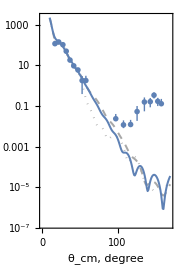

```mathematica
StringJoin[NotebookDirectory[],"/dcs/elastic1.thr"];
df=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/elastic2.thr"];
ws1=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/elastic3.thr"];
ws2=Import[%,"Table"];
ListLogPlot[{ ws1,ws2,df},Joined->True,AspectRatio->1.5,Frame->True,PlotStyle->{{gray,Dotted,thickness},{gray,Dashed,thickness},{blue,thickness}},FrameLabel->{"θ_cm, degree","dσ/dΩ, mb/sr"},ImageSize->imageSize];
heElastic=Show[%,expPlot]
```

```mathematica
Export["dcs/he_elastic.pdf",heElastic,"PDF"]
```

dcs/he_elastic.pdf

```mathematica
Sum[(0.5Interpolation[#][θ]-Interpolation[#][θ])^2/(Interpolation[#][θ]Length@expData⟦All,1⟧),{θ,expData⟦All,1⟧}]&/@{df, ws1, ws2}
```

{7.32448,5.75685,6.31289}

## Elastic transfer

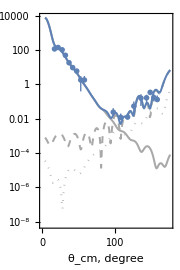

dcs/he_elastic_transfer.pdf

```mathematica
StringJoin[NotebookDirectory[],"/dcs/crossSection_3.thr"];
cs3=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_2.thr"];
cs2=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_1.thr"];
cs1=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_0.thr"];
cs0=Import[%,"Table"];
ListLogPlot[{ cs3,cs2,cs1,cs0},Joined->True,AspectRatio->1.5,Frame->True,PlotStyle->{{gray,Dotted,thickness},{gray,Dashed,thickness},{gray,thickness},{blue,thickness}},FrameLabel->{"θ_cm, degree","dσ/dΩ, mb/sr"},ImageSize->imageSize];
Show[%,expPlot]
Export["dcs/he_elastic_transfer.pdf",%,"PDF"]
```

## Lithium - 6

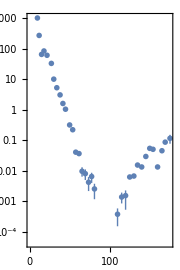

```mathematica
StringJoin[NotebookDirectory[],"/dcs/6LI4HE.exp"];
expData=Import[%,"Table"];
Map[{#⟦1⟧,Around[#⟦2⟧,{#⟦3⟧,#⟦4⟧}]}&,%];
ListLogPlot[%,IntervalMarkers->"Bars",AspectRatio->1.5,Frame->True,PlotMarkers->{Automatic, Scaled[0.035]},ImageSize->imageSize]
expPlot=%;
```

```mathematica
StringJoin[NotebookDirectory[],"/dcs/elastic_6Li1.thr"];
df=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/elastic_6Li2.thr"];
ws=Import[%,"Table"];
```

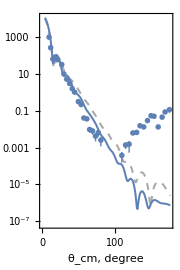

```mathematica
ListLogPlot[{ ws,df},Joined->True,AspectRatio->1.5,Frame->True,PlotStyle->{{gray,Dashed,thickness},{blue,thickness}},FrameLabel->{"θ_cm, degree","dσ/dΩ, mb/sr"},ImageSize->imageSize];
liElastic=Show[%,expPlot]
```

```mathematica
Export["dcs/li_elastic.pdf",liElastic,"PDF"]
```

dcs/li_elastic.pdf

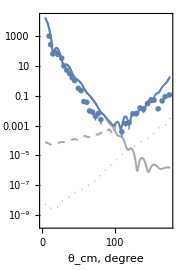

dcs/li_elastic_transfer.pdf

```mathematica
StringJoin[NotebookDirectory[],"/dcs/crossSection_3_li.thr"];
cs3=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_2_li.thr"];
cs2=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_1_li.thr"];
cs1=Import[%,"Table"];
StringJoin[NotebookDirectory[],"/dcs/crossSection_0_li.thr"];
cs0=Import[%,"Table"];
ListLogPlot[{ cs3,cs2,cs1,cs0},Joined->True,AspectRatio->1.5,Frame->True,PlotStyle->{{gray,Dotted,thickness},{gray,Dashed,thickness},{gray,thickness},{blue,thickness}},FrameLabel->{"θ_cm, degree","dσ/dΩ, mb/sr"},ImageSize->imageSize];
Show[%,expPlot]
Export["dcs/li_elastic_transfer.pdf",%,"PDF"]
```